Lecture Intro AceFEM
Notebook for Exercises 
Created by Michele Marino, Department of Civil Engineering and Computer Science, University of Rome Tor Vergata, Italy
Date: 02 November 2021 - Contact: m.marino@ing.uniroma2.it

# Element Codes

## T1LE - Linear elasticity

### Initialization

```mathematica
<<AceGen`;
SMSInitialize["T1LE","Environment"-> "AceFEM","Mode"-> "Optimal"];
SMSTemplate["SMSTopology"->"T1",
(*Numerical Integration*) "SMSDefaultIntegrationCode"->35,
(*35 -Graphics-*)
(*Initialize domain data for material parameters*)
"SMSDomainDataNames"-> {"E -Young","ν -Poisson"}, "SMSDefaultData" -> {1,0.49},
(*Expected symmetry in tangent stiffness*)
"SMSSymmetricTangent"->True,
"SMSNoElementData" -> 3];

RelevantNumbers[]:=(
nen=SMSNoNodes; 
ndim=SMSNoDimensions; 
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
(* Equivalent to: SMSInteger[es$$["id", "NoIntPoints"]] *)
)
```

### Element definitions

```mathematica
ElementDefinitions[Ig_]:=(
(*MATERIAL AND ELEMENT DATA*)
{Ee,ν}⊨SMSIO["Domain data"];

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕦IO}⊨SMSIO["All coordinates and DOFs"];
𝕦e=Flatten[𝕦IO];

(*SHAPE FUNCTIONS*)
N1⊨1-ξ-η;
N2⊨ξ;
N3⊨η;
ℕh⊨{N1, N2, N3};

(*ISOPARAMETRIC MAPPING*)
𝕏⊨SMSFreeze[ℕh.𝕏IO];
𝕁e⊨SMSD[𝕏,{ξ,η}]; 
Jed⊨SMSDet[𝕁e];

(*KINEMATICS AND CONSTITUTIVE BEHAVIOUR*)
𝕦⊨ℕh.𝕦IO;
ℍ2D⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
ℍ⊨{{ℍ2D⟦1,1⟧,ℍ2D⟦1,2⟧,0},{ℍ2D⟦2,1⟧,ℍ2D⟦2,2⟧,0},{0,0,0}};
SMSFreeze[𝔻,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];
{λ,μ}⊢SMSHookeToLame[Ee,ν];
Ψe⊨ λ/2 Tr[𝔻]^2+μ Tr[𝔻.𝔻];
)
```

### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[];

SMSDo[Ig,1,nip];

ElementDefinitions[Ig];

SMSDo[
Rgi⊨Jed wgp SMSD[Ψe,𝕦e,i];
SMSIO[Rgi,"Add to","Residual"[i]];
SMSDo[
Kgij⊨ SMSD[Rgi,𝕦e,j];
SMSIO[Kgij,"Add to","Tangent"[i,j]];
,{j,i,ndof}];
,{i,1,ndof}];
SMSEndDo[];
```

### Post-processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];

(* Initial creation on aleatory multivalue variables: total forces *)
SMSM[Fxx, 0];
SMSM[Fyy, 0];
SMSM[Fxy,0];


SMSDo[Ig,1,nip, 1, {Fxx, Fyy, Fxy} ];

ElementDefinitions[Ig];
σ⊨SMSD[Ψe,𝔻,"Symmetric"->True];

(* Creazione di nuove istanze dalle precedentemente create variabili ausiliarie *) 
SMSS[Fxx, Fxx + Jed wgp σ⟦1, 1⟧];
SMSS[Fyy, Fyy + Jed wgp σ⟦2, 2⟧];
SMSS[Fxy, Fxy + Jed wgp σ⟦1, 2⟧];


SMSIO[
{"Dxx"->𝔻⟦1,1⟧,"Dxy"->𝔻⟦1,2⟧,"Dyy"->𝔻⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧}
,"Export to","Integration point post"[Ig]]

SMSEndDo[{Fxx, Fyy, Fxy}];

SMSR[Ftxx, Fxx];
SMSR[Ftyy, Fyy];
SMSR[Ftxy, Fxy];

(* Esportazione dei 3 dati d'interesse per l'elemento come vettore riga*) 
SMSExport[{Ftxx, Ftyy, Ftxy}, Table[ed$$["Data", i], {i, 1, SMSNoElementData}]];
𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧},"Export to","Nodal point post"];
(*SMTElementData[element number, "Data"]
ed$$["Data",i]*)
```

### Code generation

```mathematica
SMSWrite[];
```

File: T1LE.c  Size: 7941  Time: 1
Method | SKR | SPP
No.Formulae | 47 | 37
No.Leafs | 781 | 633

# FEM Simulations

## Trabecular bone

```mathematica
<<AceGen`;
<<AceFEM`;
```

### Geometry

```mathematica
(* parametri geoemtrici iniziali*)
L=1.2; (*valore test*)
Dc=0.250;
Rc=Dc/2;
Nincl=25;(* tiene conto che i due spazi estremali sono la metà*)
Ninclx=Sqrt[Nincl];
Nincly=Sqrt[Nincl];
```

```mathematica
frac=0.7;
inctot=Ninclx Nincly;
Ainc=Pi*Rc^2;
AT=Ainc *inctot/frac;
L=Sqrt[AT]
Lx = L; 
Ly = L;
```

1.32405

# Definition

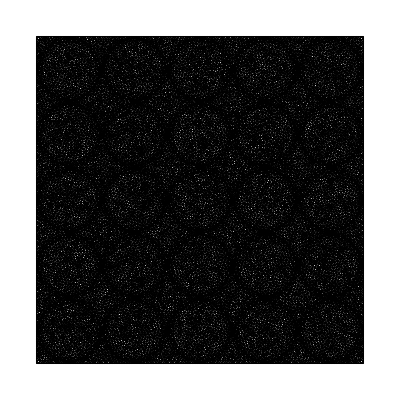

```mathematica
(* for boundary condition *)
𝔻bc = {{a,c},{c,b}};
(*a = 1;
b =0 ;
c = 0;*) 
xc=Lx/2;
yc=Ly/2;
Δx=(Lx-Dc Ninclx)/Ninclx;
Δy=(Ly-Dc Ninclx)/Ninclx;
firstxc=xc-(Δx/2)-Rc-(-1+Ninclx/2)(Dc+Δx);
firstyc=yc-(Δy/2)-Rc-(-1+Nincly/2)(Dc+Δy);
centerx=Table[firstxc+(i-1)(Dc+Δx),{i,1,Ninclx}];
centery=Table[firstyc+(i-1)(Dc+Δx),{i,1,Ninclx}];

Ωext=Rectangle[{0,0},{Lx,Ly}];
Ω=Ωext;
Do[
Ω=RegionDifference[Ω,Disk[{centerx⟦i⟧,centery⟦j⟧}, {Rc,Rc}]](*ATTENZIONE: variando i due raggi non è rispettata più la vol frac*)
,{i,1,Ninclx},{j,1,Nincly}]

marker={{{Lx/100,Ly/100},1}};
Do[
marker=Join[marker,{{{centerx⟦i⟧,centery⟦j⟧},2}}]
,{i,1,Ninclx},{j,1,Nincly}]
(*RegionPlot[Ω]*)
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1,"MaxCellMeasure"->0.0001,"MaxBoundaryCellMeasure"->0.01];
(*mesh=ToElementMesh[Ωext,"MeshOrder"->1,"RegionMarker"->{{{Lx/100,Ly/100},1}},"MeshElementType"->TriangleElement,"MaxCellMeasure"->0.01];
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1];*)
%["Wireframe"]
```

### Simulation

```mathematica
<<AceFEM`;
SMTInputData[];
domain={{"T1 matrix",3.8,0.4},{"T1 inc 1",10,0.3}};
DomainProp[domainparam_]:=(
parameter={ToString[domainparam⟦1,1⟧],"T1LE",{"E *"->domainparam⟦1,2⟧,"ν *"->domainparam⟦1,3⟧}};
Do[
parameter=Join[{parameter},{{ToString[domainparam⟦i,1⟧],"T1LE",{"E *"->domainparam⟦i,2⟧,"ν *"->domainparam⟦i,3⟧}}}]
,{i,2,Length[domainparam]}];
SMTAddDomain[
parameter
];


(*
SMTAddDomain[
{{"T1 matrix","T1LE",{"E *"-> 3.8 10^3,"ν *"->0.4}},
{"T1 inc 1","T1LE",{"E *"-> 10,"ν *"->0.3}}}
];
*)
)

(*DomainProp[domain]; *)(* definita per non dover ridefinire i parametri nella parte automatica*)
SMTAddMesh[mesh,{{"T1",1}->"T1 matrix",
{"T1",2}->"T1 inc 1"
}];

(*
SMTAddEssentialBoundary[Line[{{0,0},{0,Ly}}], 1->Function[{n, X, Y},b Y], 2 ->Function[{n, X, Y},c Y],"Set"->True];
SMTAddEssentialBoundary[Line[{{0,Ly},{Lx,Ly}}], 1 -> Function[{n, X, Y}, b*Ly+a*X], 2->Function[{n, X, Y}, c*Ly+b*X],"Set"->True];
SMTAddEssentialBoundary[Line[{{Lx,Ly},{Lx,0}}], 1 ->Function[{n, X, Y}, a*Lx+b*Y], 2->Function[{n, X, Y}, b*Lx+c*Y], "Set"->True];
SMTAddEssentialBoundary[Line[{{0,0},{Lx,0}}], 1 ->Function[{n, X, Y},a*X], 2-> Function[{n, X, Y}, b*Lx], "Set"->True];
*)
(*
SMTAnalysis[];*)
(*
SMTShowMesh["NodeMarks"->True,"BoundaryConditions"->True] *)
(*
SMTShowMesh["Mesh"->RGBColor[0,0,0],"FillElements"->{RGBColor[0.650,0.486,0.321],RGBColor[0.756,0.152,0.176]}]
SMTShowMesh["Mesh"->False,"FillElements"->{RGBColor[166,124,82],RGBColor[193,39,45]}]
*)
(* replace RGB color from report [166,124,82],[193,39,45]*)
SMTAnalysis[]
```

```mathematica
(*
MyBoundary[test_]:=(
a=test⟦1⟧;
b=test⟦2⟧;
c=test⟦3⟧;
SMTAddEssentialBoundary[Line[{{0,0},{0,Ly}}], 1->Function[{n, X, Y},b Y], 2 ->Function[{n, X, Y},c Y],"Set"->True];
SMTAddEssentialBoundary[Line[{{0,Ly},{Lx,Ly}}], 1 -> Function[{n, X, Y}, b*Ly+a*X], 2->Function[{n, X, Y}, c*Ly+b*X],"Set"->True];
SMTAddEssentialBoundary[Line[{{Lx,Ly},{Lx,0}}], 1 ->Function[{n, X, Y}, a*Lx+b*Y], 2->Function[{n, X, Y}, b*Lx+c*Y], "Set"->True];
SMTAddEssentialBoundary[Line[{{0,0},{Lx,0}}], 1 ->Function[{n, X, Y},a*X], 2-> Function[{n, X, Y}, b*Lx], "Set"->True];
)
*)
```

```mathematica
(*MyBoundary[1,0,0];*)
```

### Automatic solution

#### TEST function

function TEST

```mathematica
TEST[test_]:=(
<<AceFEM`;
SMTInputData[];
(* define material properties*)

(*domain={{"T1 matrix",5000,0.3},{"T1 inc 1",0.15,0.1}}; (*taken from lit (3800+6600/)2*)*)
Emat1=5000;
νmat1=0.3;
Emat2=5000;
νmat2=0.3;
(*
Emat2=100;
νmat2=0.1;*)

(*
Emat2=0.15;
νmat2=0.1;
*)

domain={{"T1 matrix",Emat1,νmat1},{"T1 inc 1",Emat2,νmat2}}; 
DomainProp[domain];
SMTAddMesh[mesh,{{"T1",1}->"T1 matrix",
{"T1",2}->"T1 inc 1"
}];
a=test⟦1⟧;
b=test⟦2⟧;
c=test⟦3⟧;
SMTAddEssentialBoundary[Line[{{0,0},{0,Ly}}], 1->Function[{n, X, Y},b Y], 2 ->Function[{n, X, Y},c Y],"Set"->True];
SMTAddEssentialBoundary[Line[{{0,Ly},{Lx,Ly}}], 1 -> Function[{n, X, Y}, b*Ly+a*X], 2->Function[{n, X, Y}, c*Ly+b*X],"Set"->True];
SMTAddEssentialBoundary[Line[{{Lx,Ly},{Lx,0}}], 1 ->Function[{n, X, Y}, a*Lx+b*Y], 2->Function[{n, X, Y}, b*Lx+c*Y], "Set"->True];
SMTAddEssentialBoundary[Line[{{0,0},{Lx,0}}], 1 ->Function[{n, X, Y},a*X], 2-> Function[{n, X, Y}, b*X], "Set"->True];
SMTAnalysis[];

SMTNextStep["λ"->1];
SMTNewtonIteration[];
(*Check convergence*)
SMTNewtonIteration[];
tolNR=10^-8; maxNR = 15;
SMTConvergence[tolNR,maxNR,"Analyze"];

Show[
SMTShowMesh["Field"->"σyy","DeformedMesh"->True,"Mesh"->GrayLevel[0.9]],
SMTShowMesh["FillElements"->False,"BoundaryConditions"->True,"Mesh"->GrayLevel[0]]];
area=Lx*Ly;
nel = SMTNoElements;
column=Total[Table[SMTElementData[i, "Data"], {i, nel}]]/area;
Return[column];
)

DomainProp[domainparam_]:=(
parameter={ToString[domainparam⟦1,1⟧],"T1LE",{"E *"->domainparam⟦1,2⟧,"ν *"->domainparam⟦1,3⟧}};
Do[
parameter=Join[{parameter},{{ToString[domainparam⟦i,1⟧],"T1LE",{"E *"->domainparam⟦i,2⟧,"ν *"->domainparam⟦i,3⟧}}}]
,{i,2,Length[domainparam]}];
SMTAddDomain[
parameter
];
)
```

#### Visual

```mathematica
(* visual BC*)
(*TESTx[test_]:=(
a=test⟦1⟧;
b=test⟦2⟧;
c=test⟦3⟧;
Print[test]
Print[b Y,",",c Y];
Print[b"Ly"+a*X,",",c"Ly"+b*X];
Print[a*"Lx"+b*Y,",",b*"Lx"+c*Y];
Print[a*X,",", b*X];
)
TESTx[{1,0,0}]
TESTx[{0,0.5,0}]
TESTx[{0,0,1}]*)
```

{1,0,0}

0,0

X,0

Lx,0

X,0

{0,0.5,0}

0.5 Y,0

0.5 Ly,0.5 X

0.5 Y,0.5 Lx

0,0.5 X

{0,0,1}

0,Y

0,Ly

0,Y

0,0

#### Solution

```mathematica
testBC={{1,0,0},{0,0,1},{0,0.5,0}}; (*non sono le ϵ ma valori di comodo per i parametri a,b,c per le BC tipo essenziale*)
ℂcol={{0,0,0},{0,0,0},{0,0,0}};
Do[
ℂcol⟦i⟧=TEST[testBC⟦i⟧];
,{i,1,3}]
ℂcol
ℚ=Transpose[ℂcol];
Print["R:",MatrixForm[Transpose[ℂcol]]]
𝕊=Inverse[Transpose[ℂcol]];
Print["R^-1:",MatrixForm[𝕊]]
(*
E1=1/𝕊⟦1,1⟧;(* S11=1/E1 *)
ν12=-𝕊⟦2,1⟧*(E1);(* S21=-ν12/E1 *)

G66=1/𝕊⟦3,3⟧ ;(*S66= 1/G12 *) (*G=E/2(1+ν)*)*)


(*solved=SolveValues[E1/(1 -ν12 ν21)==ℚ⟦1,1⟧&&ν12*E2/(1 -ν12 ν21)==ℚ⟦1,2⟧&&ν12*E2/(1 -ν12 ν21)==ℚ⟦2,1⟧&&E2/(1 -ν12 ν21)==ℚ⟦2,2⟧,{E1,ν12,ν21,E2}]*)
(*solved=SolveValues[E1/(1 -ν12 *ν21)==ℚ⟦1,1⟧&&ν12*E2/(1 -ν12 *ν21)==ℚ⟦1,2⟧&&E2/(1 -ν12* ν21)==ℚ⟦2,2⟧&&1-((E2/E1)*ν12^2)==(1 -ν12* ν21),{E1,ν12,ν21,E2}];*)
(*solved=SolveValues[E1/(1 -ν12 *ν21)==ℚ⟦1,1⟧&&ν12*E2/(1 -ν12 *ν21)==ℚ⟦1,2⟧&&E2/(1 -ν12* ν21)==ℚ⟦2,2⟧&&ν21/E2==ν12/E1,{E1,ν12,ν21,E2}];*)
(*solved=SolveValues[E1/(1 -ν12 *ν21)==ℚ⟦1,1⟧&&ν12*E2/(1 -ν12 *ν21)==ℚ⟦1,2⟧&&E2/(1 -ν12* ν21)==ℚ⟦2,2⟧&&1-(E2/E1)ν12^2==1-ν12*ν21,{E1,ν12,ν21,E2}];*)
(*solved=SolveValues[E1*(1-ν12)/((1 -2*ν12)(1+ν12))==ℚ⟦1,1⟧&&E1*ν12/((1 -2*ν12)(1+ν12))==ℚ⟦1,2⟧,{E1,ν12}];*)

solved1=SolveValues[E1*(1-ν12)/((1 -2*ν12)(1+ν12))==ℚ⟦1,1⟧&&E1*ν12/((1 -2*ν12)(1+ν12))==ℚ⟦1,2⟧,{E1,ν12}];
solved2=SolveValues[E2*(1-ν21)/((1 -2*ν21)(1+ν21))==ℚ⟦2,2⟧&&E2*ν21/((1 -2*ν21)(1+ν21))==ℚ⟦2,1⟧,{E2,ν21}];

EE1=solved1⟦1,1⟧;
νν12=solved1⟦1,2⟧;
νν21=solved2⟦1,2⟧;
EE2=solved2⟦1,1⟧;
Print[Subscript["E","1"],"=",EE1] 
Print[Subscript["E","2"],"=",EE2] 
Print[Subscript["ν","12"],"=",νν12] 
Print[Subscript["ν","21"],"=",νν21] 
Print[Subscript["G","12"],"=",ℚ⟦3,3⟧]     (*VERIFICA COSA SUCCEDE PER L'ANISOTROPIA*)
Print["Verifica per l'isotropia ",Subscript["G","12"],":",EE1/(2*(1+νν12))]

𝕔mat1={{(1-νmat1)Emat1/((1+νmat1)(1-2*νmat1)),(νmat1)Emat1/((1+νmat1)(1-2*νmat1)),0},{(νmat1)Emat1/((1+νmat1)(1-2*νmat1)),(1-νmat1)Emat1/((1+νmat1)(1-2*νmat1)),0},{0,0,Emat1/(2(1+νmat1))}};
𝕤mat1={{1/Emat1,-νmat1/Emat1,0},{-νmat1/Emat1,1/Emat1,0},{0,0,(2(1+νmat1))/Emat1}};
𝕔mat2={{(1-νmat2)Emat2/((1+νmat2)(1-2*νmat2)),(νmat2)Emat2/((1+νmat2)(1-2*νmat2)),0},{(νmat2)Emat2/((1+νmat2)(1-2*νmat2)),(1-νmat2)Emat2/((1+νmat2)(1-2*νmat2)),0},{0,0,Emat2/(2(1+νmat2))}};
𝕤mat2={{1/Emat2,-νmat2/Emat2,0},{-νmat2/Emat2,1/Emat2,0},{0,0,(2(1+νmat2))/Emat2}};
Print["𝕔mat1: ",MatrixForm[𝕔mat1],"  ","𝕤mat1: ",MatrixForm[𝕤mat1]]
Print["𝕔mat2: ",MatrixForm[𝕔mat2],"  ","𝕤mat2 : ",MatrixForm[𝕤mat2]]
𝕔voigt=𝕔mat1*(1-frac)+𝕔mat2*frac;
𝕤reuss=𝕤mat1*(1-frac)+𝕤mat2*frac;
Print[Subscript["𝕔","Voigt"],": ",MatrixForm[𝕔voigt]]
Print[Subscript["𝕤","Reuss"],": ",MatrixForm[𝕤reuss]]
```

{{6730.77,2884.62,-2.36002×10^-13},{2884.62,6730.77,4.38629×10^-15},{-3.50668×10^-13,-4.99062×10^-13,1923.08}}

R:(6730.77 | 2884.62 | -3.50668×10^-13
2884.62 | 6730.77 | -4.99062×10^-13
-2.36002×10^-13 | 4.38629×10^-15 | 1923.08)

R^-1:(0.000182 | -0.000078 | 1.29452×10^-20
-0.000078 | 0.000182 | 3.30081×10^-20
2.25132×10^-20 | -9.98738×10^-21 | 0.00052)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

E_1=5000.

E_2=5000.

ν_12=0.3

ν_21=0.3

G_12=1923.08

Verifica per l'isotropia G_12:1923.08

𝕔mat1: (6730.77 | 2884.62 | 0
2884.62 | 6730.77 | 0
0 | 0 | 1923.08)  𝕤mat1: (1/5000 | -0.00006 | 0
-0.00006 | 1/5000 | 0
0 | 0 | 0.00052)

𝕔mat2: (6730.77 | 2884.62 | 0
2884.62 | 6730.77 | 0
0 | 0 | 1923.08)  𝕤mat2 : (1/5000 | -0.00006 | 0
-0.00006 | 1/5000 | 0
0 | 0 | 0.00052)

𝕔_Voigt: (6730.77 | 2884.62 | 0.
2884.62 | 6730.77 | 0.
0. | 0. | 1923.08)

𝕤_Reuss: (0.0002 | -0.00006 | 0.
-0.00006 | 0.0002 | 0.
0. | 0. | 0.00052)

```mathematica
ℂ=Transpose[ℂcol]
```

{{8.14286,5.42857,-1.65656×10^-15},{5.42857,8.14286,-2.28312×10^-15},{-7.0191×10^-16,9.00775×10^-17,1.35714}}

{{EE→3.8,νν→0.4}}

# Solution algorithm (one load-step, one NR iteration)

```mathematica
SMTNextStep["λ"->1];
SMTNewtonIteration[];
(*Check convergence*)
SMTNewtonIteration[];
tolNR=10^-8; maxNR = 15;
SMTConvergence[tolNR,maxNR,"Analyze"]

Show[
SMTShowMesh["Field"->"σyy","DeformedMesh"->True,"Mesh"->GrayLevel[0.9]],
SMTShowMesh["FillElements"->False,"BoundaryConditions"->True,"Mesh"->GrayLevel[0]]
]
area=Lx*Ly;
nel = SMTNoElements;
Total[Table[SMTElementData[i, "Data"], {i, nel}]]/area
```

False

-Graphics-

{7307.69,7307.69,-3.46457×10^-13}

### Solution algorithm Homogenization

```mathematica
SMTNextStep["λ"->1];
SMTNewtonIteration[];
(*Check convergence*)
SMTNewtonIteration[];
tolNR=10^-8; maxNR = 15;
SMTConvergence[tolNR,maxNR,"Analyze"]

Show[
SMTShowMesh["Field"->"σyy","DeformedMesh"->True,"Mesh"->GrayLevel[0.9]],
SMTShowMesh["FillElements"->False,"BoundaryConditions"->True,"Mesh"->GrayLevel[0]]
]
area=Lx*Ly;
nel = SMTNoElements;
data=Total[Table[SMTElementData[i, "Data"], {i, nel}]]/area
```

False

-Graphics-

{0.,0.,0.}

(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.)

False

-Graphics-

{{0.624212,0.0880755,0.00301761},{0.624212,0.0880755,0.00301761},{0.624212,0.0880755,0.00301761}}

# Solution algorithm (one load-step, NR loop)

```mathematica
tolNR=10^-8; maxNR = 15;

SMTNextStep["λ"->1];

While[
SMTConvergence[tolNR,maxNR],
SMTNewtonIteration[];
];
area=Lx*Ly;
nel = SMTNoElements;
Total[Table[SMTElementData[i, "Data"], {i, nel}]]/area
```

# Solution algorithm (fixed load-step, NR loop)

```mathematica
(*Direct Implementation*)
tolNR=10^-8;maxNR=15;

nstep=10;   Δλ=1/nstep;

Do[
SMTNextStep["Δλ"->Δλ];
While[
SMTConvergence[tolNR,maxNR]
,SMTNewtonIteration[];
];
,{i,1,nstep}]
(*Synthetic Implementation*)
tolNR=10^-8;maxNR=15; nstep=10;   Δλ=1/nstep;

SMTEquilibriumPaths[
"Method"->"Newton"
,"λMax"->1
,"Steps"->nstep
,"Tolerance"->tolNR
,"MaxIterations"->maxNR
,"Show"->False
];
```

### Solution algorithm (fixed load-step, NR loop) - WITH POSTPROCESSING

```mathematica
tolNR=10^-8;maxNR=15;
nstep=10;   Δλ=1/nstep;
qv={{0,0}};
Do[
SMTNextStep["Δλ"->Δλ];
While[
SMTConvergence[tolNR,maxNR]
,SMTNewtonIteration[];
];
 (*Postprocessing*)
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{L,H+Wy}]]}];
,{i,1,nstep}]
qv
ListLinePlot[qv,PlotMarkers-> "●",PlotStyle->Blue]
```

# Solution algorithm (adaptive load-step, NR loop)

```mathematica
(*Direct Implementation*)
tolNR=10^-8;maxNR=50;targetNR=8;
λMax=1;λ0=λMax/10;ΔλMin=λMax/100;ΔλMax=λMax/2;

SMTNextStep["λ"->λ0];
While[
While[
step=SMTConvergence[tolNR,maxNR,{"Adaptive BC",targetNR,ΔλMin,ΔλMax,λMax}]
, SMTNewtonIteration[];
];
If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];];
step⟦3⟧ 
,If[step⟦1⟧,SMTStepBack[];];
SMTNextStep["Δλ"->step⟦2⟧]
];
(*Synthetic Implementation*)
tolNR=10^-8;maxNR=50;targetNR=8;
λMax=1;λ0=λMax/10;ΔλMin=λMax/100;ΔλMax=λMax/2;
SMTEquilibriumPaths[
"Method"->"Newton"
,"λMax"->1
,"Steps"->"Adaptive"
,"Δλ0"->λ0
,"ΔλMin"->ΔλMin
,"ΔλMax"->ΔλMax
,"Tolerance"->tolNR
,"MaxIterations"->maxNR
,"OptimalIterations"->8
,"Show"->False
];
```

# Solution algorithm (adaptive load-step, NR loop) - WITH POSTPROCESSING

```mathematica
tolNR=10^-8;maxNR=50;targetNR=8;
λMax=1;λ0=λMax/10;ΔλMin=λMax/100;ΔλMax=λMax/2;
qv={{0,0}};
SMTNextStep["λ"->λ0];
While[
While[
step=SMTConvergence[tolNR,maxNR,{"Adaptive BC",targetNR,ΔλMin,ΔλMax,λMax}]
, SMTNewtonIteration[];
];
If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];];
step⟦3⟧ 
,If[step⟦1⟧(*True if NOT converged*),
SMTStepBack[];
, (*Postprocessing*)
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{L,H+Wy}]]}];
];
SMTNextStep["Δλ"->step⟦2⟧]
];
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{L,H+Wy}]]}];
qv
ListLinePlot[qv,PlotMarkers-> "●",PlotStyle->Blue]
```